对角化后的矩阵 (Lambda): (-3 | 0
0 | -1)

特征基下的初始系数 a: {1/2,5/2}

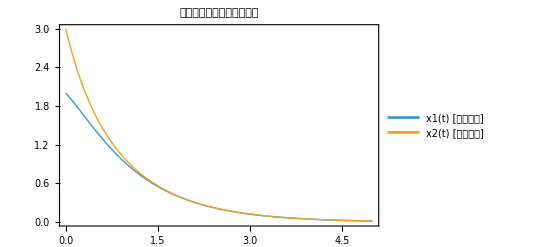

```mathematica
(*1. 定义一个耦合的线性系统矩阵 A*)(*这个矩阵代表变量 x1 和 x2 之间存在强烈的相互影响*)A={{-2,1},{1,-2}};

(*2. 计算特征值 (Eigenvalues) 和特征向量矩阵 (P)*)
{vals,vecs}=Eigensystem[A];
P=Transpose[vecs]; (*特征向量按列排列*)
invP=Inverse[P];

(*3. 验证对角化：P^-1.A.P 应得到对角阵 Lambda*)
Lambda=invP.A.P;
Print["对角化后的矩阵 (Lambda): ",Lambda//MatrixForm];

(*4. 演示向量展开与解耦求解*)
(*设定初始条件 x(0)*)
x0={2,3};

(*将初始条件 x0 投影到特征基下，求系数 a_k (即 a=P^-1.x0)*)
a=invP.x0;
Print["特征基下的初始系数 a: ",a];

(*5. 在特征空间中直接求解随时间变化的演化*)
(*在特征基下，每个分量独立演化：a_k(t)=exp(lambda_k*t)*a_k(0)*)
at[t_]:=Table[Exp[vals[[i]] t] a[[i]],{i,Length[vals]}];

(*6. 将结果转回标准基 (x=P.a)*)
xt[t_]:=P.at[t];

(*7. 绘图对比：耦合系统的时域响应*)
Plot[{xt[t][[1]],xt[t][[2]]},{t,0,5},PlotLegends->{"x1(t) [耦合变量]","x2(t) [耦合变量]"},PlotStyle->Thick,Frame->True,PlotLabel->"通过特征基解耦求解的结果"]
```